# Sezione c.

## Cose fatte prima

Creiamo un visualizzatore stupido del punto attrattivo in funzione di μ.

```mathematica
attrattivoPlot[nx_,n_,η_]:=With[{f=Function[{μ,x},μ x(1.-x)]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{0,4},{0,1}},AspectRatio->Automatic,
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
```

```mathematica
attrattivoPlot[30,10^4,10^4]
```

```mathematica
With[
{
f=Function[{μ,x},μ x(1-x)],
n=10^4,
η=10^4,
nx=30
},
Export[
"sas.csv",
Union@Flatten[
Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],
1
]
]
]
```

```mathematica
With[{a=Import["D:\\Università\\Laboratorio computazionale\\Esercizi\\01_Esame\\zzz_zoom_attrattori_contro_mu.csv"]},
ListPlot[a,PlotStyle->{AbsolutePointSize[0.015],Black},
PlotRange->{{3.4,4},{0,1}},AspectRatio->Automatic,
Ticks->{Subdivide[3.4,4.,6],Subdivide[0,1.,10]}]]
```

```mathematica
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
```

```mathematica
g[μ_,n_]:=With[{x=Solve[{z==fn[μ,z,n],0<z≤1},z,Reals]⟦1,1,2⟧},D[fn[μ,ξ,n],ξ]/.{ξ:>x}]
```

```mathematica
g[3,2]
```

```mathematica
Plot[g[μ,2],{μ,1,4}]
```

```mathematica
Plot[g[μ,4],{μ,3,4},PlotRange->{0,1}]
```

```mathematica
D[fn[3,x,2],x]/.x->2/3
```

```mathematica
Plot[{fn[3.2,x,4],x},{x,0,1},AspectRatio->Automatic]
```

```mathematica
1.9/2.9
```

```mathematica
Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]
```

```mathematica
DeleteCases[Drop[First/@Flatten[Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]/.Rule->List/.{x,y_}->y],1],_Root]
```

```mathematica
x[μ_]:=1-1/μ
x4[μ_]:=(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.{ξ->x4[μ]}]
```

```mathematica
Plot[g[μ,4]-1.,{μ,3,4},PlotRange->Full]
```

```mathematica
Flatten[Solve[g[μ,4]==1,μ,Reals]/.Rule[μ,x_]->x]//Max
```

```mathematica
Solve[{fn[μ,x,8]-x==0,μ>1+√6},x,Reals]
```

```mathematica
ClearAll[x]
```

```mathematica
With[{μ=1+√6+10^-2},Plot[{fn[μ,ξ,8]-ξ},{ξ,0,1}]]
```

```mathematica
With[{μ=1+√6+$MachineEpsilon},FindRoot[{fn[μ,ξ,8]-ξ},{ξ,0.5}]]
```

```mathematica
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.{ξ->0.43996001699979026}]
```

```mathematica
Plot[g[μ,8]-1,{μ,1+√6,3.7}]
```

```mathematica
FindRoot[FunctionInterpolation[g[μ,8]-1,{μ,1+√6,4}][μ],{μ,3.6}]
```

## Cose fatte poi

### Sezione C2.

Lemma 1. Per ogni μ>1 il punto 0 è un punto fisso repulsivo di f_μ.
Dimostrazione. Un punto fisso x_0 è repulsivo per f_μ se e solo se |f'_μ(x_0)|>1. Dal momento che f'_μ(0)=μ>1, la tesi è verificata.

```mathematica
With[
{f=Function[{μ,x},μ x(1-x)]},
D[f[μ,x],x]/.x->0
]//FullSimplify
```

Lemma 2.  Il punto fisso p_μ=1-1/μ per f_μ è attrattivo per 1<μ<3 e repulsivo per μ>3.
Dimostrazione. Con un ragionamento simile a quello usato nel Lemma 1, calcoliamo la derivata di f_μ in p_μ:

```mathematica
With[
{f=Function[{μ,x},μ x(1-x)]},
D[f[μ,x],x]/.x->1-1/μ
]//FullSimplify
```

Dato che |2-μ|<1 per 1<μ<3 e |2-μ|>1 per μ>3, si è provata la tesi.

Lemma 3. L’orbita di periodo minimo 2 di f_μ esiste per μ>3 ed è attrattiva per 3<μ<1+√6.
Dimostrazione. Se un’orbita per f_μ ha come periodo minimo 2, allora il punto iniziale x_0 è punto fisso di f_μ^2. Calcoliamo innanzitutto i punti fissi di f_μ^2:

```mathematica
With[{f=Function[{μ,x},μ x(1-x)]},Solve[{f[μ,f[μ,x]]==x,μ>0,0≤x≤1},x,Reals]]
```

Confrontando i quattro risultati ottenuti con i punti fissi di f_μ, spostiamo l’attenzione sugli ultimi due risultati, che valgono per μ>3. Calcoliamo la derivata di f_μ^2 nei punti fissi appena trovati:

```mathematica
With[{f=Function[{μ,x},μ x(1-x)]},Expand@FullSimplify[D[f[μ,f[μ,x]],x]/.(Solve[{f[μ,f[μ,x]]==x,μ>3},x,Reals]⟦{3,4}⟧/.ConditionalExpression[ξ_,_]->ξ)]]
```

e vediamo per quali μ>3 sono punti attrattivi.

```mathematica
Reduce[RealAbs[4+2 μ-μ^2]<1&&μ>3,μ,Reals]
```

E ora un disegno completamente a caso.

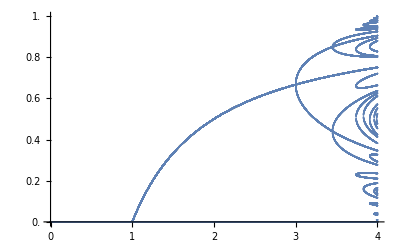

```mathematica
ListPlot[Module[{f=Function[{μ,x},μ x(1-x)],fn},
ClearAll[x];
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n];Flatten[Table[ParallelTable[{μ,x}/.NSolve[{fn[μ,x,n]==x,x≥0},x,Reals],{μ,Subdivide[0,4,10^4]}],{n,1,5}],2]],Ticks->{Range[0,4],Range[0,1,0.1]}]
```

### Sezione C3.

```mathematica
Manipulate[Plot[{fn[μ,x,n],x},{x,0,1},AspectRatio->Automatic],{{μ,2.9},0,4},{{n,2},2^Range[0,10]},Initialization:>{fn[μ_,x_,n_]:=Nest[(μ #(1-#))&,x,n]}]
```